# F 2 : Calcul d’angle de torsion : Calculs et graphisme

## 4V118 Acides Nucléiques : de la molécule unique à la cellule

## I. Quelques exercices pour faire des graphiques

### 1. Représenter un point dans le plan

Point[], est une primitive graphique.
D’autres primitives sont Line[], Circle[], Disk[], Rectangle[], ... et quelques autres
a. Utiliser la fonction Point[] que l’on cherchera dans l’aide, pour faire un point à l’écran.

```mathematica
Graphics[Point[{0,0}]]
```

-Graphics-

b. Faire maintenant un point rouge

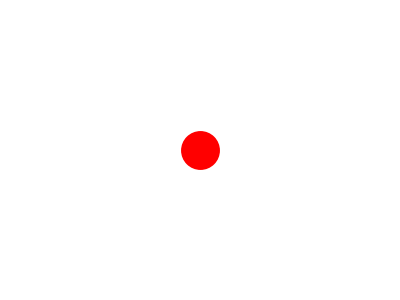

```mathematica
Graphics[{Red,PointSize[0.07],Point[{0,0}]}]
```

c. Contrôler la présentation du graphique avec Show[]

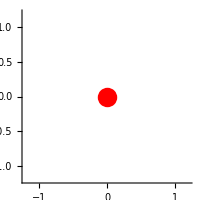

```mathematica
Show[Graphics[{Red,PointSize[0.07],Point[{0,0}]}],Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->200]
```

### 2. Faire une fonction de rotation

a. Déclarer un point sur l’axe y en tapant, et en validant : pointM={0,1}

```mathematica
pointM={0,1}
```

{0,1}

b. Faire une matrice de rotation à l’aide du menu :

```mathematica
matRot[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
```

```mathematica
matRot[250]
```

{{Cos[250],-Sin[250]},{Sin[250],Cos[250]}}

```mathematica
matRot[α].pointM/.{α->π/3}
matRot[α].pointM/.{α->π/4}
```

{-(√3)/2,1/2}

{-1/(√2),1/(√2)}

### 3. Faire tourner un point dans le plan

a. Faire un graphique (avec Show[], et Graphics[], comme dans la partie I.1 pour tracer un segment rouge tournée de π/3 avec Line[]:

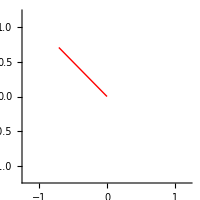

```mathematica
Show[Graphics[{Red,Line[{{0,0},matRot[α].pointM}]}],Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->200]/.{α->π/4}
```

b. Utiliser Manipulate[] pour faire tourner le point M en faisant varier q entre 0 et 2 Pi

```mathematica
Manipulate[Show[Graphics[{Red,Line[{{0,0},matRot[α].pointM}]}],Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImageSize->200],{α,0,2π}]
```

### 4. Faire tourner un point en 3D

```mathematica
matRot3D[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 1, 1}})
```

a. Utiliser Manipulate[] pour faire tourner le point3DM={0,1,0} entre 0 et 2 Pi

```mathematica
point3DM={80,1,0}
```

{80,1,0}

```mathematica
Manipulate[Show[Graphics3D[{Red,Line[{{0,0,0},matRot3D[α].point3DM}]}],Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}},ImageSize->200],{α,0,2π}]
```

## II. Recherche de l’expression de l’angle de torsion

### I./ Les outils graphiques pour contrôler les essais

1./ Le cadre de l’expérimentation et de construction

```mathematica
pointA[θ_,zA_]:={Cos[θ],Sin[θ],zA}
pointB={0,0,0}
pointC={0,0,1}
pointD[xD_,zD_]:={xD,0,zD}
```

{0,0,0}

{0,0,1}

2./ a. Représentation

```mathematica
Show[Graphics3D[{Red,Line[{pointA[θ,zA],pointB}],Red,Line[{pointB,pointC}],Red,Line[{pointC,pointD[xD,zD]}]}],Axes->True,PlotRange->{{0,1},{-2,2},{0,2}},ImageSize->200]/.{θ->0,zA->0,xD->1,zD->2}
```

-Graphics3D-

2./  b. Application 2

```mathematica
Show[Graphics3D[{Red,Thick,Line[{pointA[θ,zA],pointB}],Blue,Thick,Line[{pointB,pointC}],Blue,Thick,Line[{pointC,pointD[xD,zD]}]}],Axes->True,PlotRange->{{0,1},{-2,2},{0,2}},ImageSize->200]/.{θ->0,zA->0,xD->1,zD->2}
```

-Graphics3D-

2./ c. Axe et échelles, Labels, et cadrage :

```mathematica
Show[Graphics3D[{Red,Thick,Line[{pointA[θ,zA],pointB}],Blue,Thick,Line[{pointB,pointC}],Blue,Thick,Line[{pointC,pointD[xD,zD]}]}],Axes->True,AxesLabel->{x,y,z},AxesEdge->{{1,1},{1,-1},{-1,1}},PlotRange->{{0,1},{-2,2},{0,2}},ImageSize->200]/.{θ->0,zA->0,xD->1,zD->2}
```

-Graphics3D-

3./ d. Tracer (à part) d’un cylindre (pour mieux voir les rotations ensuite)

```mathematica
Graphics3D[{Cylinder[{{0,0,0},{0,0,1}},1]}]
```

-Graphics3D-

3./ e. Transparence du cylindre

```mathematica
Graphics3D[{Opacity[0.1],Cylinder[{{0,0,0},{0,0,1}},1]}]
```

-Graphics3D-

3./ f. Assemblage des segments joignant ABCD et du cylindre :

```mathematica
Graphics3D[{Red,Thick,Line[{pointA[θ,zA],pointB}],Blue,Thick,Line[{pointB,pointC}],Blue,Thick,Line[{pointC,pointD[xD,zD]}],Opacity[0.1],Cylinder[{{0,0,0},{0,0,1}},1]}]/.{θ-> 0,zA->0,xD->1,zD->2}
```

-Graphics3D-

3./ g. Manipulate

```mathematica
Manipulate[Show[Graphics3D[{Red,Thick,Line[{pointA[θ,0],pointB}],Blue,Thick,Line[{pointB,pointC}],Blue,Thick,Line[{pointC,pointD[1,2]}],Opacity[0.1],Cylinder[{{0,0,0},{0,0,1}},1]}],Axes->True,AxesLabel->{x,y,z},AxesEdge->{{1,1},{1,-1},{-1,1}},ImageSize->200],{θ,0,2π}]
```

### 2./ Calcul d’un angle de torsion

1./ Vecteur perpendiculaire à un plan : Produit vectoriel

```mathematica
Cross[pointB-pointA[θ,zA],pointC-pointB]
```

{-Sin[θ],Cos[θ],0}

```mathematica
Cross[pointC-pointB,pointD[xD,zD]-pointC](*Arrow*)
```

{0,xD,0}

```mathematica
Graphics3D[{Red,Thick,Arrow[{pointC,pointB}]}]
Graphics3D[{Red,Thick,Arrow[{pointA[0,1],pointD[1,2]}]}]
```

-Graphics3D-

-Graphics3D-

2./ Mettre l’ensemble de tout ce qui a été fait dans un même dessin avec Show[],
puis mettre le tout dans Manipulate[] :
Une petite animation permet de comprendre que tout va bien :

```mathematica
Manipulate[Show[Graphics3D[{Red,Thick,Line[{pointA[θ,0],pointB}],Blue,Thick,Line[{pointB,pointC}],Blue,Thick,Line[{pointC,pointD[xD,zD]}],Opacity[0.1],Cylinder[{{0,0,0},{0,0,1}},1],Brown,Thick,Arrow[{pointB,{0,1,0}}],Green,Thick,Arrow[{{0,0,0},pointA[θ+π/2,0]}]}],Axes->True,AxesLabel->{x,y,z},AxesEdge->{{1,1},{1,-1},{-1,1}},ImageSize->200],{θ,0,4π},{xD,1,2},{zD,2,3}]
```

### 2./ Expression cherchée

L’expression suivante renvoie un angle, qcal, compris entre -180° et +180°

```mathematica
OverVector[BA] = pointB - pointA[π/4,2]
OverVector[CD] = pointC - pointD[1,2]
OverVector[BC] = pointB -pointC
```

{-1/(√2),-1/(√2),-2}

{-1,0,-1}

{0,0,-1}

```mathematica
Sign[OverVector[BA]/Norm[OverVector[BA]]×OverVector[CD]/Norm[OverVector[CD]].(OverVector[BC]/Norm[OverVector[BC]])]
ArcCos[((OverVector[BA]×OverVector[BC])/Norm[OverVector[BA]×OverVector[BC]]).((OverVector[CD]×OverVector[BC])/Norm[OverVector[CD]×OverVector[BC]])]*180/π
```

1

45

### 3./ Fonction complète en Mathematica

(Pour les plus courageux), écrire la fonction donnant l’angle de torsion à partir des points A, B, C, et D.
Conseil : Utiliser des With[] pour structurer chaque étape de l’écriture de votre fonction.

```mathematica
ArcCos[({1,0,0}.{0,1,0})/(Norm[{1,0,0}]*Norm[{0,1,0}])]
torsion[pA_,pB_,pC_,pD_]:=With[{BA=pB-pA,CD=pC-pD},ArcCos[(BA.CD)/(Norm[BA]*Norm[CD])]]//N
torsion[pointA[π/4,2],pointB,pointC,pointD[1,2]]
```

π/2

0.543194

### 4./ Vérifier que q choisi est bien retrouvé correctement avec qcal

Conseil (Pour les plus courageux) :
Pour afficher du texte sous un graphique, j’ai utilisé :

```mathematica
Manipulate[Column[{
Show[Graphics3D[{Red,Thick,Line[{pointA[θ,0],pointB}],Blue,Thick,Line[{pointB,pointC}],Blue,Thick,Line[{pointC,pointD[xD,zD]}],Opacity[0.1],Cylinder[{{0,0,0},{0,0,1}},1],Brown,Thick,Arrow[{pointB,{0,1,0}}],Green,Thick,Arrow[{{0,0,0},pointA[θ+π/2,0]}]}],Axes->True,AxesLabel->{x,y,z},AxesEdge->{{1,1},{1,-1},{-1,1}},ImageSize->200],
Text[Style["θcal = "<>ToString[torsion[pointA[θ,1],pointB,pointC,pointD[xD,zD]]]<>"θ="<>ToString[θ*180/π],Red,16
]
]
}],{θ,0,4π},{xD,1,2},{zD,2,3}]
```